```mathematica
(*Mathematica*)
```

```mathematica
Clear[p,pa]
```

```mathematica
(*Vertex Complex polynomials ;even middle polygon: 3-2*n-3*)
```

```mathematica
pa[x_,-1]=0.3535533905932737 z^2+z^5
```

0.353553 z^2+z^5

```mathematica
pa[z_,0]=1-5*z^2-5*z^4+z^6 (*octahedron*)
```

1-5 z^2-5 z^4+z^6

```mathematica
pa[z_,0.5]=1-6* z^2+ z^3+ z^4-6* z^5+z^7
```

1-6 z^2+z^3+z^4-6 z^5+z^7

```mathematica
pa[z_,1]=1- z^2-4 z^3+4 z^5- z^6+z^8
```

1-z^2-4 z^3+4 z^5-z^6+z^8

```mathematica
pa[z_,1.5]=1-3.47213595499958 z^3-3.472135954999577 z^6+z^9
```

1-3.47214 z^3-3.47214 z^6+z^9

```mathematica
pa[z_,2]=1-4 z^3- z^4- z^6+4 z^7+z^10
```

1-4 z^3-z^4-z^6+4 z^7+z^10

```mathematica
pa[z_,3]=-1+4.4721359549995805 z^3-4.472135954999578 z^9+z^12
```

-1+4.47214 z^3-4.47214 z^9+z^12

```mathematica
pa[z_,4]=-1+4.4721359549995805 z^3- z^6+ z^8-4.472135954999577 z^11+z^14
```

-1+4.47214 z^3-z^6+z^8-4.47214 z^11+z^14

```mathematica
pa[z_,5]=-1+4.472135954999584 z^3-z^6+ z^10-4.472135954999574 z^13+z^16
```

-1+4.47214 z^3-z^6+z^10-4.47214 z^13+z^16

```mathematica
pa[z_,6]=-1+4.472135954999586 z^3- z^6+ z^12-4.472135954999564 z^15+z^18
```

-1.+4.47214 z^3-z^6+z^12-4.47214 z^15+z^18

```mathematica
(*renormalization of 1-3-1 to 3-4-3 polynomials as Herman rings Julia*)
```

```mathematica
p[z_]=z^2*pa[z,2]/pa[z,-1]^2
```

(z^2 (1-4 z^3-z^4-z^6+4 z^7+z^10))/((0.353553 z^2+z^5)^2)

```mathematica
w=x/.NSolve[p[x]==0,x]
```

{0.809017-1.40126 ⅈ,0.809017+1.40126 ⅈ,-1.61803,1.,-1.,0.-1. ⅈ,0.+1. ⅈ,-0.309017-0.535233 ⅈ,-0.309017+0.535233 ⅈ,0.618034}

```mathematica
max=Max[Norm/@w]+1
```

2.61803

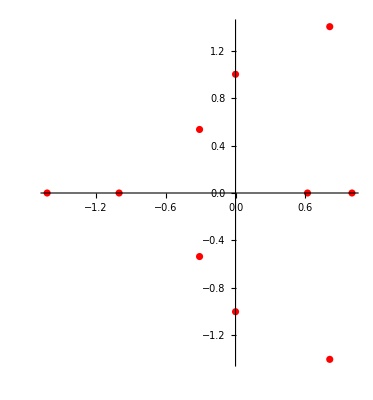

```mathematica
ComplexListPlot[w,PlotStyle->Red,ImageSize->Full]
```

```mathematica
ga=ComplexPlot[p[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000];
```

```mathematica
gb=ComplexPlot3D[p[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000];
```

```mathematica
g1=JuliaSetPlot[p[z]/3,z,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
```

```mathematica
g2=ListPlot[JuliaSetPoints[p[z]/3,z],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_Herman_rings2nd_131_to_343_scale3_grid.jpg",GraphicsGrid[{{ga,gb},{g1,g2}},ImageSize->{4000,4000}]]
```

Julia_Herman_rings2nd_131_to_343_scale3_grid.jpg

```mathematica
(*end*)
```